```mathematica
M[x_] := ({{1, x}, {x, -1}})
```

```mathematica
Eigensystem[M[x]]
```

{{-√(1+x^2),√(1+x^2)},{{-(-1+√(1+x^2))/x,1},{-(-1-√(1+x^2))/x,1}}}

```mathematica
H = ({{Subscript[ω, 1]-I Subscript[γ, 1], g}, {g, Subscript[ω, 2]-I Subscript[γ, 2]}});
```

```mathematica
FullSimplify[Eigensystem[H]]
```

{{1/2 (-ⅈ γ_1-ⅈ γ_2+ω_1-√((2 g+γ_1-γ_2+ⅈ ω_1-ⅈ ω_2) (2 g-γ_1+γ_2-ⅈ ω_1+ⅈ ω_2))+ω_2),1/2 (-ⅈ γ_1-ⅈ γ_2+ω_1+√((2 g+γ_1-γ_2+ⅈ ω_1-ⅈ ω_2) (2 g-γ_1+γ_2-ⅈ ω_1+ⅈ ω_2))+ω_2)},{{-(ⅈ γ_1-ⅈ γ_2-ω_1+√((2 g+γ_1-γ_2+ⅈ ω_1-ⅈ ω_2) (2 g-γ_1+γ_2-ⅈ ω_1+ⅈ ω_2))+ω_2)/(2 g),1},{(-ⅈ γ_1+ⅈ γ_2+ω_1+√((2 g+γ_1-γ_2+ⅈ ω_1-ⅈ ω_2) (2 g-γ_1+γ_2-ⅈ ω_1+ⅈ ω_2))-ω_2)/(2 g),1}}}

```mathematica
SubPlus[y][x_, μ_, γ_] := Sqrt[μ^2 + (x + I γ)^2]
SubMinus[y][x_,μ_,γ_] := -Sqrt[μ^2+(x+I γ)^2]
```

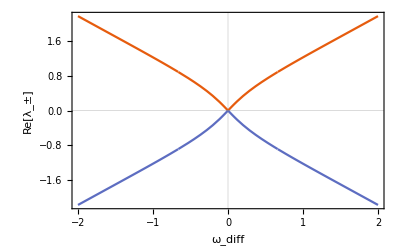

```mathematica
Plot[{Re[SubPlus[y][x, 1, 1.2]], Re[SubMinus[y][x,1,1.2]]}, {x, -2, 2}, PlotTheme->"Scientific", FrameLabel->{"ω_diff","Re[λ_±]"}]
```

```mathematica
Plot3D[Re[SubPlus[y][x,1, γ]],{x,-2,2},{γ, 0.5, 1.5},PlotTheme->"Scientific", PlotPoints->40]
```